```mathematica
Clear["Global`*"]
```

```mathematica
dimdgl={2 m l^2 ϕ1''[t]+m l^2 ϕ2''[t] Cos[ϕ1[t]-ϕ2[t]]+m l^2 ϕ2'[t]^2 Sin[ϕ1[t]-ϕ2[t]]+2 m g l Sin[ϕ1[t]],m l^2 ϕ2''[t]+m l^2 ϕ1''[t] Cos[ϕ1[t]-ϕ2[t]]-m l^2 ϕ1'[t]^2 Sin[ϕ1[t]-ϕ2[t]]+m g l Sin[ϕ2[t]]};
```

```mathematica
Simplify[dimdgl/(m g l)/.{ϕ1'[t]->√(g/l) ϕ1'[t],ϕ1''[t]->g/l ϕ1''[t],ϕ2'[t]->√(g/l) ϕ2'[t],ϕ2''[t]->g/l ϕ2''[t]}]
```

{2 Sin[ϕ1[t]]+Sin[ϕ1[t]-ϕ2[t]] ϕ2'[t]^2+2 ϕ1''[t]+Cos[ϕ1[t]-ϕ2[t]] ϕ2''[t],Sin[ϕ2[t]]-Sin[ϕ1[t]-ϕ2[t]] ϕ1'[t]^2+Cos[ϕ1[t]-ϕ2[t]] ϕ1''[t]+ϕ2''[t]}

```mathematica
dgl={2 ϕ1''[t]+ϕ2''[t] Cos[ϕ1[t]-ϕ2[t]]+ϕ2'[t]^2 Sin[ϕ1[t]-ϕ2[t]]==-2 Sin[ϕ1[t]],ϕ2''[t]+ϕ1''[t] Cos[ϕ1[t]-ϕ2[t]]-ϕ1'[t]^2 Sin[ϕ1[t]-ϕ2[t]]==-Sin[ϕ2[t]]};
ab1={ϕ1[0]==0,ϕ2[0]==1,ϕ1'[0]==1,ϕ2'[0]==0};
ab2={ϕ1[0]==-.5,ϕ2[0]==.6,ϕ1'[0]==0,ϕ2'[0]==1.44236};
```

```mathematica
sol[ab_]:=NDSolve[{dgl,ab},{ϕ1,ϕ2},{t,0,100}][[1]];
```

```mathematica
sol1=sol[ab1];
sol2=sol[ab2];
```

```mathematica
e[t_]=-Cos[ϕ1[t]]-(Cos[ϕ1[t]]+Cos[ϕ2[t]])+(D[Cos[ϕ1[t]],t]^2+D[Sin[ϕ1[t]],t]^2)/2+(D[Cos[ϕ1[t]]+Cos[ϕ2[t]],t]^2+D[Sin[ϕ1[t]]+Sin[ϕ2[t]],t]^2)/2;
plotEnergy[sol_]:=Plot[Evaluate[Abs[e[0]-e[t]]/.sol],{t,0,100}]
```

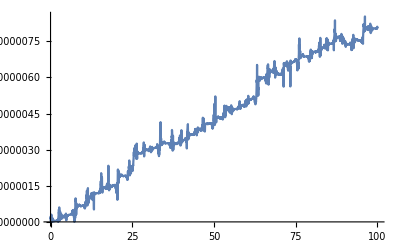

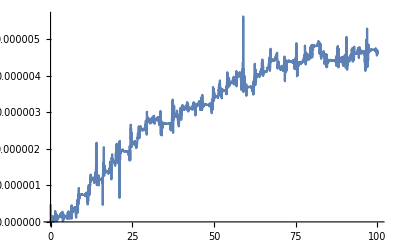

```mathematica
plotEnergy[sol1]
plotEnergy[sol2]
```

```mathematica
animate[sol_]:=Animate[Graphics[{PointSize[.1],Line[{{0,0},{Sin[ϕ1[t]],-Cos[ϕ1[t]]}/.sol}],Point[{Sin[ϕ1[t]],-Cos[ϕ1[t]]}/.sol],Line[{{Sin[ϕ1[t]],-Cos[ϕ1[t]]},{Sin[ϕ1[t]]+Sin[ϕ2[t]],-Cos[ϕ1[t]]-Cos[ϕ2[t]]}}/.sol],Point[{Sin[ϕ1[t]]+Sin[ϕ2[t]],-Cos[ϕ1[t]]-Cos[ϕ2[t]]}/.sol]},PlotRange->{{-2.1,2.1},{-2.1,2.1}}],{t,0,100},DefaultDuration->50,AnimationRunning->False]
```

```mathematica
animate[sol1]
animate[sol2]
```

```mathematica
poincare[ab_]:=ListPlot[Reap[NDSolve[{dgl,ab,WhenEvent[ϕ1'[t]==0,Sow[{ϕ1[t],ϕ2[t]}]]},{ϕ1,ϕ2},{t,0,20000}]][[2,1]]]
```

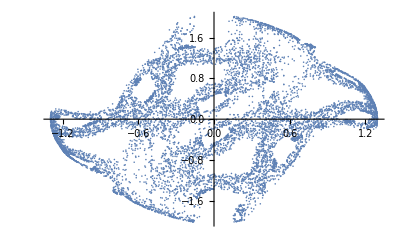

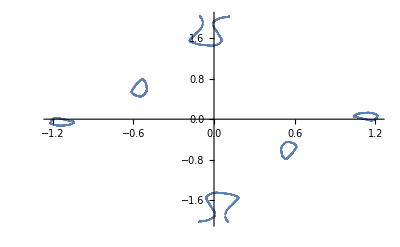

```mathematica
poincare[ab1]
poincare[ab2]
```